```mathematica
Eq = (emax-emax*enot)*(Exp[-gamma*x] + enot);
Manipulate[
Plot[Eq/.{emax->EMAX,gamma->0.01,enot->0.2},{x,0,1000},PlotRange->{0,1}],
{EMAX,0,1}]
```

```mathematica
FullSimplify[Eq]
```

(ⅇ^(-gamma x)+enot) (emax-emax enot)

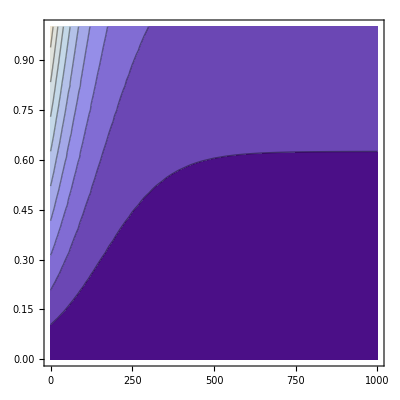

```mathematica
ContourPlot[Eq/.{gamma->0.01,enot->0.2},{x,0,1000},{emax,0,1},PlotRange->{0,1}]
```